# Efficiency Comparison RobustAD Data

## Methods

```mathematica
SetDirectory[NotebookDirectory[]];
paretoEffsDir = "pareto_effs";
```

```mathematica
strategyOrder = {"cvar25", "stability", "cap", "wasserstein", "consistency"};
boxStrategyOrder = {"cvar25", "stability", "cap", "wasserstein", "consistency"};
strategyMaximizeQ = <|"cvar25" -> True, "cvar10" -> True, "cap" -> True,
   "stability" -> False, "wasserstein" -> False, "consistency" -> True|>;
strategyStudyObj = <|"cvar25" -> "cvar25eff", "cvar10" -> "cvar10eff",
   "cap" -> "cap", "stability" -> "drift", "wasserstein" -> "wasserstein", "consistency" -> "consistency"|>;
strategyPretty = <|"cvar25" -> "semi-supervised", "cvar10" -> "semi-sup (CVaR10)",
   "cap" -> "CAP", "stability" -> "stable", "wasserstein" -> "wasserstein", "consistency" -> "consistency"|>;
strategyBoxColors = <|"cvar25" -> "#3f90da", "stability" -> "#ffa90e",
   "cap" -> "#bd1f01", "wasserstein" -> "#832db6", "consistency" -> "#94a4a2"|>;
```

```mathematica
(* Background/reference datasets excluded from the signal mean. No bare
   "shifted": robustad signals are shifted_anomaly_*, its background
   shifted_normal_all is caught via "normal". *)
bkgDatasetQ[ds_String] :=
  StringContainsQ[ds, "normal" | "SingleNeutrino" | "ZB_" | "reference"];

(* Original 250 Hz picks, from ORIGINAL_PICKS/VERBATIM_FALLBACKS in
   scripts/make_pareto_scripts.py (cvar25eff -> cvar25, drift -> stability). *)
originalPicks = <|
   "physics" -> <|
     "ae" -> <|"cap" -> 175, "cvar25" -> 169, "stability" -> 564, "wasserstein" -> 584|>,
     "vae" -> <|"cap" -> 179, "cvar25" -> 345, "stability" -> 529, "wasserstein" -> 539|>,
     "dsae" -> <|"cap" -> 570, "cvar25" -> 599, "stability" -> 565, "wasserstein" -> 383|>,
     "dsvae" -> <|"cap" -> 324, "cvar25" -> 372, "stability" -> 445, "wasserstein" -> 503|>,
     "svdd" -> <|"cap" -> 536, "cvar25" -> 739, "stability" -> 419, "wasserstein" -> 545|>,
     "realnvp" -> <|"cap" -> 376, "cvar25" -> 523, "stability" -> 505, "wasserstein" -> 383|>|>,
   "cifar10" -> <|
     "ae" -> <|"cap" -> 211, "cvar25" -> 592, "stability" -> 241, "wasserstein" -> 279|>,
     "vae" -> <|"cap" -> 520, "cvar25" -> 568, "stability" -> 587, "wasserstein" -> 596|>,
     "svdd" -> <|"cap" -> 599, "cvar25" -> 284, "stability" -> 191, "wasserstein" -> 266|>,
     "realnvp" -> <|"cap" -> 211, "cvar25" -> 535, "stability" -> 104, "wasserstein" -> 475|>|>,
   "robustad" -> <|
     "ae" -> <|"cap" -> 350, "cvar25" -> 526, "stability" -> 568, "wasserstein" -> 299|>,
     "vae" -> <|"cap" -> 402, "cvar25" -> 62, "stability" -> 389, "wasserstein" -> 587|>,
     "svdd" -> <|"cap" -> 546, "cvar25" -> 518, "stability" -> 525, "wasserstein" -> 581|>,
     "realnvp" -> <|"cap" -> 174, "cvar25" -> 333, "stability" -> 478, "wasserstein" -> 591|>|>|>;

numOrMissing[x_] := If[NumericQ[x], N[x], Missing["NA"]];
```

```mathematica
rebuttalDomain = "robustad";
rebuttalFrontsDir = "paretos/robustad";
rebuttalOutDir = "effs_robustad/";
rebuttalTierSuffix = "";
rebuttalModelExps = <|"AE" -> "robustad_ae_pareto", "VAE" -> "robustad_vae_pareto", "SVDD" -> "robustad_svdd_pareto", "RealNVP" -> "robustad_realnvp_pareto", "DTE" -> "robustad_dte_pareto"|>;
```

## Data Import

```mathematica
strategyContextQ[strat_String, ctx_String] :=
  StringStartsQ[ctx, "summary/eff/"] &&
   With[{m = StringDrop[ctx, StringLength["summary/eff/"]]},
    Switch[strat,
     "cvar25", m === "cvar25_ema/max",
     "cvar10", m === "cvar10_ema/max",
     "cap", StringStartsQ[m, "cap_ema"] && StringEndsQ[m, "/max"],
     "consistency", StringStartsQ[m, "consistency_ema"] && StringEndsQ[m, "/max"],
     "stability", StringContainsQ[m, "drift_ema"] && StringEndsQ[m, "/min"],
     "wasserstein", StringContainsQ[m, "w1dist_ema"] && StringEndsQ[m, "/min"],
     _, False]];

(* Per-signal eval columns: eff_<label>_<dataset>, excluding the eff_med_ /
   eff_min_ summaries; the plain eff_<label> scalar is the shortest prefix. *)
perSignalCols[hdr_List] := Module[{eff, base, cols},
  eff = Select[hdr, StringQ[#] && StringStartsQ[#, "eff_"] &&
      !StringStartsQ[#, "eff_med_"] && !StringStartsQ[#, "eff_min_"] &];
  base = SelectFirst[SortBy[eff, StringLength],
    Function[b, Count[eff, c_ /; StringStartsQ[c, b <> "_"]] >= 3]];
  cols = Select[eff, StringStartsQ[#, base <> "_"] &];
  <|"cols" -> cols,
    "names" -> (StringDrop[#, StringLength[base] + 1] & /@ cols)|>];

(* One record per run: strategy, Q' (optimized_main), Q'' (optimized_sec),
   per-signal TEST efficiencies at the run's own strategy checkpoint, and
   their mean over signal datasets. *)
loadRuns[exp_String] := Module[
  {raw, hdr, idx, rows, runs = <||>, eraw, ehdr, eidx, erows, ps, rn, strat,
   arr, sig},
  raw = Import[FileNameJoin[{paretoEffsDir, exp <> ".csv"}], "CSV"];
  hdr = First[raw]; rows = Rest[raw];
  idx = AssociationThread[hdr -> Range[Length[hdr]]];
  Do[If[row[[idx["ckpt"]]] === "strategy",
    runs[row[[idx["run_name"]]]] = <|
      "strategy" -> row[[idx["strategy"]]],
      "q0" -> numOrMissing[row[[idx["optimized_main"]]]],
      "q1" -> numOrMissing[row[[idx["optimized_sec"]]]]|>],
   {row, rows}];
  eraw = Import[FileNameJoin[{paretoEffsDir, exp <> "_eval.csv"}], "CSV"];
  ehdr = First[eraw]; erows = Rest[eraw];
  eidx = AssociationThread[ehdr -> Range[Length[ehdr]]];
  ps = perSignalCols[ehdr];
  Do[
   rn = row[[eidx["run_name"]]];
   If[KeyExistsQ[runs, rn] && row[[eidx["split"]]] === "test" &&
     strategyContextQ[runs[rn]["strategy"], row[[eidx["context"]]]],
    arr = AssociationThread[ps["names"] ->
       (numOrMissing[row[[eidx[#]]]] & /@ ps["cols"])];
    sig = DeleteMissing[KeySelect[arr, !bkgDatasetQ[#] &]];
    If[Length[sig] > 0,
     runs[rn] = Join[runs[rn],
       <|"testArr" -> sig, "eff" -> Mean[Values[sig]]|>]]],
   {row, erows}];
  runs];

frontsOf[runs_Association] := GroupBy[runs, #["strategy"] &];
```

## Pareto Selection Rules

```mathematica
(* argmax/argmin over name-sorted candidates: first best wins (deterministic,
   mirrors the reference implementation). *)
argBest[vals_Association, maximize_] := Module[{names, best},
  names = Sort[Keys[vals]];
  best = If[maximize, Max[Values[vals]], Min[Values[vals]]];
  SelectFirst[names, vals[#] == best &]];

oraclePick[front_Association] :=
  argBest[DeleteMissing[#["eff"] & /@ front], True];

(* Pick functions share the signature pickF[front, strat, model]. *)
bestQPick[front_Association, strat_String, model_:None] := Module[{q},
  q = Select[front, !MissingQ[#["q0"]] && !MissingQ[#["eff"]] &];
  If[Length[q] == 0, Missing["NoData"],
   argBest[#["q0"] & /@ q, strategyMaximizeQ[strat]]]];

(* Knee: goodness-orient both recomputed objectives over ALL retrained front
   points (they constitute the search front), min-max normalise, take the
   point of maximal distance from the chord joining the endpoints. *)
kneePick[front_Association, strat_String, model_:None] := Module[
  {maximize0 = strategyMaximizeQ[strat], usable, g, distinct, lo0, hi0,
   lo1, hi1, norm, order, e1, e2, chord, best = Missing["Degenerate"],
   bestD = -1., d},
  usable = Select[front,
    !MissingQ[#["q0"]] && !MissingQ[#["q1"]] && !MissingQ[#["eff"]] &];
  If[Length[usable] < 3, Return[Missing["Degenerate"]]];
  g = KeyValueMap[{#1, If[maximize0, #2["q0"], -#2["q0"]], -#2["q1"]} &,
    KeySort[usable]];
  distinct = DeleteDuplicates[g[[All, 2 ;; 3]]];
  If[Length[distinct] < 3, Return[Missing["Degenerate"]]];
  lo0 = Min[g[[All, 2]]]; hi0 = Max[g[[All, 2]]];
  lo1 = Min[g[[All, 3]]]; hi1 = Max[g[[All, 3]]];
  If[hi0 == lo0 || hi1 == lo1, Return[Missing["Degenerate"]]];
  norm = {#[[1]], (#[[2]] - lo0)/(hi0 - lo0), (#[[3]] - lo1)/(hi1 - lo1)} & /@
    g;
  order = SortBy[norm, {#[[2]], #[[3]]} &];
  e1 = order[[1, 2 ;; 3]]; e2 = order[[-1, 2 ;; 3]];
  chord = Norm[e2 - e1];
  If[chord == 0, Return[Missing["Degenerate"]]];
  Do[
   d = Abs[(e2[[1]] - e1[[1]])*(e1[[2]] - p[[3]]) -
       (e1[[1]] - p[[2]])*(e2[[2]] - e1[[2]])]/chord;
   If[d > bestD, bestD = d; best = p[[1]]],
   {p, order[[2 ;; -2]]}];
  best];

(* Spearman rho between goodness-oriented Q' and the mean test efficiency. *)
frontSpearman[front_Association, strat_String] := Module[{usable, qs, effs, rho},
  usable = KeySort[Select[front, !MissingQ[#["q0"]] && !MissingQ[#["eff"]] &]];
  If[Length[usable] < 3, Return[Missing["TooFew"]]];
  qs = If[strategyMaximizeQ[strat], #, -#] &[Values[#["q0"] & /@ usable]];
  effs = Values[#["eff"] & /@ usable];
  rho = Quiet[Check[N[SpearmanRho[qs, effs]], Missing["Undefined"]]];
  If[NumericQ[rho], rho, Missing["Undefined"]]];
```

## Plots

```mathematica
(* --- rule box-plot grid ------------------------------------------------ *)

(* Legacy per-model box plot (verbatim from the Plotting Method section of
   effs_physics.nb) + a grid assembling one panel per model for a given
   picking rule. Strategies absent under a rule (degenerate fronts) are
   drawn as collapsed (all-zero) boxes, the legacy convention. *)
hexColors = {"#3f90da", "#ffa90e", "#bd1f01", "#94a4a2", "#832db6",
   "#a96b59", "#e76300", "#b9ac70", "#717581", "#92dadd"};
makeBoxCMS[data_, labels_, yLabel_, cmsPos_, tevPos_, precY_:1, xLabelY_:0.06, modelLabel_:"AE", modelLabelPos_:{0.639, 0.899}] := Module[{majorLen, minorLen, makeTicks01, yVals, yTicks, yTicksRight, plot, cmsText, tevText, plotLeft = 0.01, plotBottom = 0.12, plotWidth = 0.98, plotHeight = 0.84, xCenters}, majorLen = Scaled[0.015]; minorLen = Scaled[0.015/2]; makeTicks01[{(vmin_)?NumericQ, (vmax_)?NumericQ}, prec_] := Module[{maj, min}, maj = N[FindDivisions[{vmin, vmax}, 6]]; min = N[Flatten[Table[Most[Rest[Subdivide[maj[[k]], maj[[k + 1]], 6]]], {k, 1, Length[maj] - 1}]]]; Join[({#1, NumberForm[#1, {6, prec}], {majorLen, 0}} & ) /@ maj, ({#1, "", {minorLen, 0}} & ) /@ min]]; yVals = Flatten[data]; yTicks = makeTicks01[{0, 1.05*Max[yVals]}, precY]; yTicksRight = yTicks /. {v_, _, len_} :> {v, "", len}; nBoxes = Length[data]; q10 = (Quantile[#1, 0.1] & ) /@ data; q90 = (Quantile[#1, 0.9] & ) /@ data; xPos = Range[nBoxes]; p10p90Graphics = Table[{EdgeForm[None], FaceForm[Directive[RGBColor["#92dadd"], Opacity[0.22]]], Rectangle[{xPos[[i]] - 0.39, q10[[i]]}, {xPos[[i]] + 0.39, q90[[i]]}]}, {i, nBoxes}]; plot = BoxWhiskerChart[data, {"Outliers", {"MedianMarker", 1., Directive[RGBColor["#94a4a2"], AbsoluteThickness[3], Opacity[2]]}, {"Whiskers", Directive[Black, AbsoluteThickness[3]]}, {"Fences", 0.5, Directive[Black, AbsoluteThickness[2]]}, {"MeanMarker", 0.78, Directive[Black, Opacity[1], AbsoluteThickness[3]]}, {"MeanDiamond", 0.8, Directive[RGBColor["#92dadd"], Opacity[0.4]]}, {"Outliers", Graphics[{RGBColor["#3f90da"], Rectangle[{-1, -1}, {1, 1}]}]}}, Prolog -> p10p90Graphics, BarSpacing -> 0.3, ChartStyle -> Table[Directive[RGBColor["#3f90da"], Opacity[0.8]], {Length[data]}], Frame -> True, Axes -> False, FrameTicks -> {{yTicks, yTicksRight}, {Automatic, Automatic}}, FrameStyle -> Directive[Black, AbsoluteThickness[2]], FrameTicksStyle -> Directive[Black, FontSize -> 22, FontFamily -> "TeX Gyre Heros"], LabelStyle -> Directive[Black, FontSize -> 24, FontFamily -> "TeX Gyre Heros"], FrameLabel -> {None, Style[yLabel, Black, FontSize -> 30, FontFamily -> "TeX Gyre Heros"]}, GridLines -> {None, Automatic}, GridLinesStyle -> Directive[GrayLevel[0.85], AbsoluteThickness[1.5]], ImageSize -> 1300, AspectRatio -> 0.65, ImagePadding -> {{100, 40}, {40, 40}}, PlotRange -> {0, 1.05*Max[yVals]}, PlotRangePadding -> {{Scaled[-0.1], Scaled[-0.03]}, {Scaled[0.03], Scaled[0.01]}}]; cmsText = Row[{Style["CMS", Bold, FontFamily -> "TeX Gyre Heros", 24], Style[" Simulation Preliminary", Italic, FontFamily -> "TeX Gyre Heros", 24]}]; tevText = Style["14 TeV", FontFamily -> "TeX Gyre Heros", 24]; xCenters = {0.165, 0.3, 0.43, 0.57}; Graphics[Join[{Inset[plot, Scaled[{plotLeft, plotBottom}], {Left, Bottom}, Scaled[{plotWidth, plotHeight}]]}, Table[Inset[Style[labels[[i]], FontFamily -> "TeX Gyre Heros", 22], Scaled[{xCenters[[i]], xLabelY}], {Center, Top}], {i, Length[labels]}], {Inset[cmsText, Scaled[cmsPos], {Left, Bottom}], Inset[tevText, Scaled[tevPos], {Right, Bottom}], Inset[Framed[Style[modelLabel, FontFamily -> "TeX Gyre Heros", Italic, 32, Black], Background -> White, FrameStyle -> Directive[Black, AbsoluteThickness[1.5]], RoundingRadius -> 0, FrameMargins -> {{8, 8}, {4, 4}}], Scaled[modelLabelPos], {Right, Top}]}], PlotRange -> {{0, 1}, {0, 1}}, AspectRatio -> 0.5, ImageSize -> 1300]]

makeRuleBoxGrid[groups_Association, ncols_Integer, mag_:0.55] := Module[{panels},
  panels = KeyValueMap[Function[{modelLabel, sub}, Module[{len, data},
      If[Length[sub] == 0, Nothing,
       len = Length[First[Values[sub]]];
       data = Table[If[KeyExistsQ[sub, s], sub[s],
          ConstantArray[0., len]], {s, boxStrategyOrder}];
       makeBoxCMS[data,
        {"semi-supervised", "stable", "CAP", "wasserstein"},
        "Efficiency (%)", {0.085, 0.9}, {0.64, 0.9}, 1, 0.17,
        modelLabel]]]], groups];
  (* Panels are built at full legacy scale (1300 pt each) so fonts and label
     positions keep the exact original proportions; Magnify then shrinks the
     assembled grid uniformly. *)
  Magnify[GraphicsGrid[Partition[panels, UpTo[ncols]],
    ImageSize -> {1300*ncols, Automatic},
    Spacings -> {Scaled[0.01], Scaled[0.01]}], mag]];
```

```mathematica
(* --- optimisation-front plot --------------------------------------------- *)

secObjLabel = <|"mse" -> "MSE", "mseq99" -> "MSE", "kl" -> "KL",
   "dist" -> "dist", "logp" -> "-log p"|>;

studyFile[frontsDir_String, model_String, strat_String] := Module[{cands},
  cands = Select[FileNames[
     model <> "_" <> strategyStudyObj[strat] <> "_vs_*.csv", frontsDir],
    !StringContainsQ[#, "q99"] && !StringContainsQ[#, "exploration"] &];
  If[cands === {}, Missing["NoStudy"], First[Sort[cands]]]];

makeFrontPlot[frontsDir_String, model_String, strat_String,
   modelLabel_String] := Module[
  {file, raw, hdr, idx, rows, pts, front, dom, secName, xlab, ylab},
  file = studyFile[frontsDir, model, strat];
  If[MissingQ[file], Return[Missing["NoStudy"]]];
  raw = Import[file, "CSV"];
  hdr = First[raw]; rows = Rest[raw];
  idx = AssociationThread[hdr -> Range[Length[hdr]]];
  pts = Select[rows, NumericQ[#[[idx["values_0"]]]] &&
      NumericQ[#[[idx["values_1"]]]] &];
  front = Select[pts, ToString[#[[idx["is_pareto"]]]] === "True" &];
  dom = Select[pts, ToString[#[[idx["is_pareto"]]]] =!= "True" &];
  secName = StringReplace[FileBaseName[file],
    {model <> "_" <> strategyStudyObj[strat] <> "_vs_" -> "", "_b16k" -> ""}];
  xlab = strategyPretty[strat] <> " objective";
  ylab = Lookup[secObjLabel, secName, secName];
  ListPlot[
   {dom[[All, {idx["values_0"], idx["values_1"]}]],
    front[[All, {idx["values_0"], idx["values_1"]}]]},
   PlotStyle -> {Directive[GrayLevel[0.75], PointSize[0.008]],
     Directive[RGBColor["#bd1f01"], PointSize[0.014]]},
   Frame -> True, Axes -> False,
   FrameStyle -> Directive[Black, AbsoluteThickness[1.5]],
   FrameTicksStyle -> Directive[Black, FontSize -> 16,
     FontFamily -> "TeX Gyre Heros"],
   FrameLabel -> {Style[xlab, 18, FontFamily -> "TeX Gyre Heros"],
     Style[ylab, 18, FontFamily -> "TeX Gyre Heros"]},
   PlotLabel -> Style[modelLabel <> ": " <> strategyPretty[strat], 18,
     FontFamily -> "TeX Gyre Heros"],
   ImageSize -> 420, AspectRatio -> 0.8,
   PlotRangePadding -> Scaled[0.05]]];

modelFrontRow[frontsDir_String, model_String, modelLabel_String] :=
  Module[{plots},
   plots = DeleteMissing[
     makeFrontPlot[frontsDir, model, #, modelLabel] & /@
      {"cvar25", "stability", "cap", "wasserstein"}];
   If[plots === {}, Missing["NoStudies"], GraphicsRow[plots,
     ImageSize -> 420*Length[plots], Spacings -> 0]]];
```

## Tables

```mathematica
(* Key translation between the rebuttal strategy names and the legacy
   association keys used by BuildLatexTableCompactAsymCollapse. Missing
   strategies are zero-filled (the legacy collapsed-method convention). *)
legacyStratKey = <|"cvar25" -> "semisupervised", "stability" -> "stable",
   "cap" -> "CAP", "wasserstein" -> "wasserstein", "consistency" -> "consistency"|>;
toLegacyGroups[groups_Association] := Association @@ KeyValueMap[
   Function[{m, sub}, Module[
     {len = If[Length[sub] > 0, Length[First[Values[sub]]], 1]},
     m -> Association @@ Table[
        legacyStratKey[s] -> If[KeyExistsQ[sub, s], N[sub[s]],
          ConstantArray[-1., len]], {s, boxStrategyOrder}]]],
   dropEmptyModels[groups]];
```

```mathematica
ClearAll[BootstrapPairedDiffCI, WilcoxonSignedRankPExact, SafeWilcoxonP, CollapsedMethodQ, FormatNum, FormatP, FormatMeanOrDash, FormatAsymPMOrDash, ArchitectureRowDataCompactCollapse, LatexRowCompactAsymCollapse, BuildArchitectureRowsCompactCollapse, BuildLatexTableCompactAsymCollapse]; 

CollapsedMethodQ[x_List] := AllTrue[x, #1 == 0. & ]; 

BootstrapPairedDiffCI[a_List, b_List, nBoot_:10000, alpha_:0.05] := Module[{n, diffs, boots}, If[Length[a] =!= Length[b], Return[Missing["LengthMismatch"]]]; n = Length[a]; diffs = a - b; boots = Table[Mean[RandomChoice[diffs, n]], {nBoot}]; Quantile[boots, {alpha/2, 1 - alpha/2}]]; 

WilcoxonSignedRankPExact[a_List, b_List] := Module[{d, absd, sgn, n, order, sortedAbs, sortedIdx, ranks, groups, start, wPlus, allSums, pLeft, pRight}, If[Length[a] =!= Length[b], Return[Missing["LengthMismatch"]]]; d = DeleteCases[a - b, 0.]; If[d === {}, Return[1.]]; absd = Abs[d]; sgn = Sign[d]; n = Length[d]; order = Ordering[absd]; sortedAbs = absd[[order]]; sortedIdx = order; ranks = ConstantArray[0., n]; groups = Split[Range[n], sortedAbs[[#1]] == sortedAbs[[#2]] & ]; start = 1; Do[Module[{len = Length[g], mid}, mid = Mean[Range[start, start + len - 1]]; ranks[[sortedIdx[[g]]]] = mid; start += len; ], {g, groups}]; wPlus = Total[Pick[ranks, sgn, 1]]; allSums = Total /@ (Pick[ranks, #1, 1] & ) /@ Tuples[{0, 1}, n]; pLeft = N[Count[allSums, x_ /; x <= wPlus]/Length[allSums]]; pRight = N[Count[allSums, x_ /; x >= wPlus]/Length[allSums]]; Min[1., 2.*Min[pLeft, pRight]]]; 

SafeWilcoxonP[a_List, b_List] := WilcoxonSignedRankPExact[a, b]; 

FormatNum[x_, digits_:2] := ToString[NumberForm[x, {Infinity, digits}, NumberPadding -> {"", "0"}, NumberPoint -> "."]]; 

FormatP[p_] := Which[MissingQ[p], "-", p < 0.001, "<0.001", True, ToString[NumberForm[p, {Infinity, 3}, NumberPadding -> {"", "0"}, NumberPoint -> "."]]]; 

FormatMeanOrDash[x_List, digits_:2] := If[CollapsedMethodQ[x], "-", FormatNum[Mean[x], digits]]; 

FormatAsymPMOrDash[center_, ci_, digits_:2] := Module[{lower, upper}, If[MissingQ[center] || MissingQ[ci], Return["-"]]; lower = center - ci[[1]]; upper = ci[[2]] - center; StringJoin["$", FormatNum[center, digits], "^{+", FormatNum[upper, digits], "}", "_{-", FormatNum[lower, digits], "}$"]]; 

ArchitectureRowDataCompactCollapse[archName_String, methods_Association, nBoot_:10000, alpha_:0.05] := Module[{semi, cap, stable, w1, semiCollapsed, capCollapsed, stableCollapsed, w1Collapsed, dCS, dCW, ciCS, ciCW, pCS, pCW}, semi = methods["semisupervised"]; cap = methods["CAP"]; stable = methods["stable"]; w1 = methods["wasserstein"]; If[ !Length[semi] == Length[cap] == Length[stable] == Length[w1], Return[Association["Architecture" -> archName, "Error" -> "All method arrays must have equal lengths."]]]; semiCollapsed = CollapsedMethodQ[semi]; capCollapsed = CollapsedMethodQ[cap]; stableCollapsed = CollapsedMethodQ[stable]; w1Collapsed = CollapsedMethodQ[w1]; dCS = If[capCollapsed || stableCollapsed, Missing["Collapsed"], Mean[cap - stable]]; dCW = If[capCollapsed || w1Collapsed, Missing["Collapsed"], Mean[cap - w1]]; ciCS = If[capCollapsed || stableCollapsed, Missing["Collapsed"], BootstrapPairedDiffCI[cap, stable, nBoot, alpha]]; ciCW = If[capCollapsed || w1Collapsed, Missing["Collapsed"], BootstrapPairedDiffCI[cap, w1, nBoot, alpha]]; pCS = If[capCollapsed || stableCollapsed, Missing["Collapsed"], SafeWilcoxonP[cap, stable]]; pCW = If[capCollapsed || w1Collapsed, Missing["Collapsed"], SafeWilcoxonP[cap, w1]]; Association["Architecture" -> archName, "Semi" -> semi, "CAP" -> cap, "Stable" -> stable, "W1" -> w1, "CAPMinusStable" -> dCS, "CAPMinusStableCI" -> ciCS, "CAPMinusStableP" -> pCS, "CAPMinusW1" -> dCW, "CAPMinusW1CI" -> ciCW, "CAPMinusW1P" -> pCW]]; 

LatexRowCompactAsymCollapse[row_Association, digits_:2] := StringJoin[StringRiffle[{row["Architecture"], FormatMeanOrDash[row["Semi"], digits], FormatMeanOrDash[row["CAP"], digits], FormatMeanOrDash[row["Stable"], digits], FormatMeanOrDash[row["W1"], digits], FormatAsymPMOrDash[row["CAPMinusStable"], row["CAPMinusStableCI"], digits], FormatP[row["CAPMinusStableP"]], FormatAsymPMOrDash[row["CAPMinusW1"], row["CAPMinusW1CI"], digits], FormatP[row["CAPMinusW1P"]]}, " & "], " \\\\"]; 

BuildArchitectureRowsCompactCollapse[allArchitectures_Association, nBoot_:10000, alpha_:0.05] := KeyValueMap[ArchitectureRowDataCompactCollapse[#1, #2, nBoot, alpha] & , allArchitectures]; 

BuildLatexTableCompactAsymCollapse[allArchitectures_Association, nBoot_:10000, alpha_:0.05, digits_:2] := Module[{rows, body}, rows = BuildArchitectureRowsCompactCollapse[allArchitectures, nBoot, alpha]; body = StringRiffle[(LatexRowCompactAsymCollapse[#1, digits] & ) /@ rows, "\n"]; StringJoin["\\begin{tabular}{lcccccccc}\n", "\\toprule\n", "Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n", "\\midrule\n", body, "\n", "\\bottomrule\n", "\\end{tabular}"]];
```

```mathematica
(* Markdown twins of the table builders. The legacy-format pair works from
   pre-built rows (BuildArchitectureRowsCompactCollapse) so LaTeX and
   markdown show identical bootstrap CIs. *)
MarkdownRowCompactAsymCollapse[row_Association, digits_:2] :=
  StringJoin["| ", StringRiffle[{row["Architecture"],
      FormatMeanOrDash[row["Semi"], digits],
      FormatMeanOrDash[row["CAP"], digits],
      FormatMeanOrDash[row["Stable"], digits],
      FormatMeanOrDash[row["W1"], digits],
      FormatAsymPMOrDash[row["CAPMinusStable"], row["CAPMinusStableCI"],
       digits], FormatP[row["CAPMinusStableP"]],
      FormatAsymPMOrDash[row["CAPMinusW1"], row["CAPMinusW1CI"], digits],
      FormatP[row["CAPMinusW1P"]]}, " | "], " |"];

LatexTableFromRows[rows_List, digits_:2] := StringJoin[
   "\\begin{tabular}{lcccccccc}\n\\toprule\n",
   "Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n",
   "\\midrule\n",
   StringRiffle[LatexRowCompactAsymCollapse[#, digits] & /@ rows, "\n"],
   "\n\\bottomrule\n\\end{tabular}"];

MarkdownTableFromRows[rows_List, digits_:2] := StringJoin[
   "| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |\n",
   "|---|---|---|---|---|---|---|---|---|\n",
   StringRiffle[MarkdownRowCompactAsymCollapse[#, digits] & /@ rows, "\n"]];

ruleTableMarkdown[rows_List, ruleLabel_String] := StringJoin[
   "| Arch. | Strategy | n | Pick | eff | Oracle | eff_or | d_or | Orig. | ",
   "eff_o | d_o |\n|---|---|---|---|---|---|---|---|---|---|---|\n",
   StringRiffle[
    "| " <> StringRiffle[{#["model"], strategyPretty[#["strategy"]],
         ToString[#["n"]], fmtTrial[#["pick"]], fmtEffPct[#["pickEff"]],
         fmtTrial[#["oracle"]], fmtEffPct[#["oracleEff"]],
         fmtDelta[#["pickEff"], #["oracleEff"]], fmtTrial[#["orig"]],
         fmtEffPct[#["origEff"]],
         fmtDelta[#["pickEff"], #["origEff"]]}, " | "] <> " |" & /@ rows,
    "\n"]];

spearmanTableMarkdown[modelExps_Association, domain_String] :=
  Module[{rows = {}},
   Do[Module[{model = modelKey, runs, fronts},
     runs = rebuttalRuns[modelExps[modelKey]];
     fronts = frontsOf[runs];
     Do[If[KeyExistsQ[fronts, strat], Module[{front = fronts[strat], rho},
        rho = frontSpearman[front, strat];
        AppendTo[rows, {model, strategyPretty[strat],
          ToString[Length[front]],
          If[NumericQ[rho], fmtNum[rho, 2], "-"]}]]],
      {strat, strategyOrder}]],
    {modelKey, Keys[modelExps]}];
   StringJoin["| Arch. | Strategy | n | rho |\n|---|---|---|---|\n",
    StringRiffle[("| " <> StringRiffle[#, " | "] <> " |") & /@ rows,
     "\n"]]];


(* Compact Spearman matrix: one row per architecture, one column per training
   strategy (legacy order); cell = rho (n), with n the number of front points
   entering the ranking. "-" = strategy absent; "- (n)" = rho undefined
   (n < 3 or tied/zero-variance efficiencies). *)
spearmanDisplayOrder = {"cvar25", "cap", "stability", "wasserstein"};
spearmanCellString[fronts_Association, strat_String] := Module[{front, usable, rho},
  If[!KeyExistsQ[fronts, strat], Return["-"]];
  front = fronts[strat];
  usable = Select[front, !MissingQ[#["q0"]] && !MissingQ[#["eff"]] &];
  rho = frontSpearman[front, strat];
  StringJoin[If[NumericQ[rho], fmtNum[rho, 2], "-"], " (",
   ToString[Length[usable]], ")"]];
spearmanMatrixCells[modelExps_Association] := Table[
   Prepend[Table[spearmanCellString[frontsOf[rebuttalRuns[modelExps[m]]], s],
     {s, spearmanDisplayOrder}], m], {m, Keys[modelExps]}];
spearmanMatrixLatex[modelExps_Association] := StringJoin[
   "\\begin{tabular}{lcccc}\n\\toprule\n",
   "Arch. & Semi & CAP & Stable & W1 \\\\\n\\midrule\n",
   StringRiffle[StringRiffle[#, " & "] <> " \\\\" & /@
     spearmanMatrixCells[modelExps], "\n"],
   "\n\\bottomrule\n\\end{tabular}"];
spearmanMatrixMarkdown[modelExps_Association] := StringJoin[
   "| Arch. | Semi | CAP | Stable | W1 |\n|---|---|---|---|---|\n",
   StringRiffle[("| " <> StringRiffle[#, " | "] <> " |") & /@
     spearmanMatrixCells[modelExps], "\n"]];
```

```mathematica
(* Holm-Bonferroni step-down correction applied jointly to all Wilcoxon
   p-values of one table -- the benchmark's family of comparisons (2 tests
   per architecture row; 12 for physics, 8 for cifar10/robustad). Raw
   p-values are kept under <key>Raw. *)
HolmAdjustRows[rows_List] := Module[
  {keys = {"CAPMinusStableP", "CAPMinusW1P"}, idx = {}, ps, m, order,
   run = 0., newRows = rows, i, k, adj},
  Do[If[NumericQ[Lookup[newRows[[a]], b]], AppendTo[idx, {a, b}]],
   {a, Length[newRows]}, {b, keys}];
  m = Length[idx];
  If[m == 0, Return[newRows]];
  ps = Lookup[newRows[[#[[1]]]], #[[2]]] & /@ idx;
  order = Ordering[ps];
  Do[
   {i, k} = idx[[order[[j]]]];
   adj = Min[1., (m - j + 1)*ps[[order[[j]]]]];
   run = Max[run, adj];
   newRows[[i]] = Join[newRows[[i]],
     Association[k <> "Raw" -> ps[[order[[j]]]], k -> run]],
   {j, m}];
  newRows];

(* Corrected builders: every table generated through these prints
   Holm-adjusted p-values (overrides the raw legacy definition). *)
BuildLatexTableCompactAsymCollapse[allArchitectures_Association,
   nBoot_:10000, alpha_:0.05, digits_:2] :=
  LatexTableFromRows[HolmAdjustRows[
    BuildArchitectureRowsCompactCollapse[allArchitectures, nBoot, alpha]],
   digits];
BuildMarkdownTableCompactAsymCollapse[allArchitectures_Association,
   nBoot_:10000, alpha_:0.05, digits_:2] :=
  MarkdownTableFromRows[HolmAdjustRows[
    BuildArchitectureRowsCompactCollapse[allArchitectures, nBoot, alpha]],
   digits];
```

```mathematica
(* Rebuttal axes over the legacy data.
   Axis 1 (LHC): both operating points side by side in one table; the Holm
   family is per operating point (12 tests), consistent with the main tables.
   Axis 2 (CIFAR10/RobustAD): compact per-model summary + counts over the
   AUPRC comparisons, backing a text paragraph. Stars mark Holm-adjusted
   p < 0.05; collapsed comparisons render as n/a. *)
axisPair[row_Association, dkey_String, pkey_String, latexQ_] := Module[
  {d = Lookup[row, dkey], p = Lookup[row, pkey], star},
  If[!NumericQ[d] || !NumericQ[p], Return[{"n/a", "-"}]];
  star = If[p < 0.05, If[latexQ, "$^{*}$", "*"], ""];
  {fmtNum[d, 2], FormatP[p] <> star}];

QuantileAxisCells[assocTail_Association, assocQ99_Association, latexQ_,
   nBoot_:10000, alpha_:0.05] := Module[
  {rT = HolmAdjustRows[
     BuildArchitectureRowsCompactCollapse[assocTail, nBoot, alpha]],
   rQ = HolmAdjustRows[
     BuildArchitectureRowsCompactCollapse[assocQ99, nBoot, alpha]]},
  MapThread[Function[{a, b}, Join[{a["Architecture"]},
     axisPair[a, "CAPMinusStable", "CAPMinusStableP", latexQ],
     axisPair[a, "CAPMinusW1", "CAPMinusW1P", latexQ],
     axisPair[b, "CAPMinusStable", "CAPMinusStableP", latexQ],
     axisPair[b, "CAPMinusW1", "CAPMinusW1P", latexQ]]], {rT, rQ}]];

QuantileAxisLatex[assocTail_Association, assocQ99_Association,
   nBoot_:10000, alpha_:0.05] := StringJoin[
  "\\begin{tabular}{lcccccccc}\n\\toprule\n",
  " & \\multicolumn{4}{c}{$q \\approx 0.999991$ (250\\,Hz)} & ",
  "\\multicolumn{4}{c}{$q = 0.99$} \\\\\n",
  "Arch. & $\\Delta_{\\mathrm{C-S}}$ & $p$ & $\\Delta_{\\mathrm{C-W}}$ & $p$ & ",
  "$\\Delta_{\\mathrm{C-S}}$ & $p$ & $\\Delta_{\\mathrm{C-W}}$ & $p$ \\\\\n\\midrule\n",
  StringRiffle[StringRiffle[#, " & "] <> " \\\\" & /@
    QuantileAxisCells[assocTail, assocQ99, True, nBoot, alpha], "\n"],
  "\n\\bottomrule\n\\end{tabular}"];

QuantileAxisMarkdown[assocTail_Association, assocQ99_Association,
   nBoot_:10000, alpha_:0.05] := StringJoin[
  "| Arch. | d(C-S) tail | p | d(C-W) tail | p | d(C-S) q99 | p | ",
  "d(C-W) q99 | p |\n|---|---|---|---|---|---|---|---|---|\n",
  StringRiffle[("| " <> StringRiffle[#, " | "] <> " |") & /@
    QuantileAxisCells[assocTail, assocQ99, False, nBoot, alpha], "\n"]];

MetricAxisSummary[assoc_Association, label_String:"AUPRC",
   nBoot_:10000, alpha_:0.05] := Module[
  {rows = HolmAdjustRows[
     BuildArchitectureRowsCompactCollapse[assoc, nBoot, alpha]],
   lines = {}, sigFor = 0, sigAgainst = 0, na = 0, bestCells = 0,
   tally, fmtDP},
  tally[d_, p_] := Which[!NumericQ[d] || !NumericQ[p], na++,
    d > 0 && p < 0.05, sigFor++, d < 0 && p < 0.05, sigAgainst++,
    True, Null];
  fmtDP[d_, p_] := If[!NumericQ[d] || !NumericQ[p], "n/a",
    fmtNum[d, 2] <> " (" <> FormatP[p] <>
     If[p < 0.05, "*", ""] <> ")"];
  Do[Module[{cap = Mean[r["CAP"]], st = Mean[r["Stable"]],
     w1 = Mean[r["W1"]], best},
    best = cap >= st && cap >= w1;
    If[best, bestCells++];
    tally[Lookup[r, "CAPMinusStable"], Lookup[r, "CAPMinusStableP"]];
    tally[Lookup[r, "CAPMinusW1"], Lookup[r, "CAPMinusW1P"]];
    AppendTo[lines, StringJoin["| ", r["Architecture"], " | ",
      fmtNum[cap, 2], If[best, " (best)", ""], " | ",
      fmtDP[Lookup[r, "CAPMinusStable"], Lookup[r, "CAPMinusStableP"]],
      " | ",
      fmtDP[Lookup[r, "CAPMinusW1"], Lookup[r, "CAPMinusW1P"]], " |"]]],
   {r, rows}];
  StringJoin["Axis 2 (", label, ") summary -- ",
   "star = Holm-adjusted p < 0.05, family = this table:\n",
   "| Arch. | CAP | d CAP-Stable (p) | d CAP-W1 (p) |\n",
   "|---|---|---|---|\n", StringRiffle[lines, "\n"], "\n",
   "counts: CAP best point estimate in ", ToString[bestCells], "/",
   ToString[Length[rows]], " cells; significant for CAP: ",
   ToString[sigFor], ", against: ", ToString[sigAgainst], ", n/a: ",
   ToString[na], " (of ", ToString[2*Length[rows]], " comparisons)."]];
```

## Formatting

```mathematica
fmtNum[x_, digits_:2] := If[NumericQ[x],
   ToString[NumberForm[N[x], {Infinity, digits}, NumberPadding -> {"", "0"},
     NumberPoint -> "."]], "-"];
fmtEffPct[x_] := If[NumericQ[x], fmtNum[100*x, 2], "-"];
fmtTrial[name_] := If[StringQ[name],
   Last[StringSplit[name, "_t"]], "-"];
fmtDelta[x_, ref_] := If[NumericQ[x] && NumericQ[ref],
   fmtNum[100*(x - ref), 2], "-"];

(* One rule-table row per (model, strategy) front. pickF[front, strat] must
   return a run name (or Missing). *)
ruleTableRows[modelExps_Association, domain_String, pickF_] := Module[{rows = {}},
  Do[Module[{model = modelKey, exp = modelExps[modelKey], runs, fronts},
    runs = rebuttalRuns[exp];
    fronts = frontsOf[runs];
    Do[If[KeyExistsQ[fronts, strat], Module[
       {front = fronts[strat], pick, oracle, orig, origTrial, effOf},
       effOf[name_] := If[StringQ[name] && KeyExistsQ[front, name],
         front[name]["eff"], Missing["NA"]];
       pick = pickF[front, strat, model];
       oracle = oraclePick[front];
       origTrial = Query[ToLowerCase[model], strat][
         Lookup[originalPicks, domain, <||>]];
       orig = If[IntegerQ[origTrial],
         strat <> "_t" <> ToString[origTrial], Missing["NA"]];
       AppendTo[rows, <|"model" -> model, "strategy" -> strat,
         "n" -> Length[front], "pick" -> pick, "pickEff" -> effOf[pick],
         "pickQ" -> If[StringQ[pick], front[pick]["q0"], Missing["NA"]],
         "oracle" -> oracle, "oracleEff" -> effOf[oracle],
         "orig" -> orig, "origEff" -> effOf[orig]|>]]],
     {strat, strategyOrder}]],
   {modelKey, Keys[modelExps]}];
  rows];

ruleTableLatex[rows_List, ruleLabel_String] := Module[{body},
  body = StringRiffle[
    StringRiffle[{#["model"], strategyPretty[#["strategy"]],
        ToString[#["n"]], fmtTrial[#["pick"]], fmtEffPct[#["pickEff"]],
        fmtTrial[#["oracle"]], fmtEffPct[#["oracleEff"]],
        fmtDelta[#["pickEff"], #["oracleEff"]],
        fmtTrial[#["orig"]], fmtEffPct[#["origEff"]],
        fmtDelta[#["pickEff"], #["origEff"]]}, " & "] <> " \\\\" & /@ rows,
    "\n"];
  StringJoin["% rule: ", ruleLabel, "\n",
   "\\begin{tabular}{llccccccccc}\n\\toprule\n",
   "Arch. & Strategy & $n$ & Pick & $\\langle\\varepsilon\\rangle$ & ",
   "Oracle & $\\langle\\varepsilon\\rangle_{\\mathrm{or}}$ & $\\Delta_{\\mathrm{or}}$ & ",
   "Orig. & $\\langle\\varepsilon\\rangle_{\\mathrm{o}}$ & $\\Delta_{\\mathrm{o}}$ \\\\\n",
   "\\midrule\n", body, "\n\\bottomrule\n\\end{tabular}"]];

spearmanTableLatex[modelExps_Association, domain_String] := Module[{rows = {}},
  Do[Module[{model = modelKey, runs, fronts},
    runs = rebuttalRuns[modelExps[modelKey]];
    fronts = frontsOf[runs];
    Do[If[KeyExistsQ[fronts, strat], Module[{front = fronts[strat], rho},
       rho = frontSpearman[front, strat];
       AppendTo[rows, <|"model" -> model, "strategy" -> strat,
         "n" -> Length[front],
         "rho" -> If[NumericQ[rho], fmtNum[rho, 2], "-"]|>]]],
     {strat, strategyOrder}]],
   {modelKey, Keys[modelExps]}];
  StringJoin["\\begin{tabular}{llcc}\n\\toprule\n",
   "Arch. & Strategy & $n$ & $\\rho_{\\mathrm{Spearman}}$ \\\\\n\\midrule\n",
   StringRiffle[
    StringRiffle[{#["model"], strategyPretty[#["strategy"]], ToString[#["n"]],
        #["rho"]}, " & "] <> " \\\\" & /@ rows, "\n"],
   "\n\\bottomrule\n\\end{tabular}"]];
```

```mathematica
(* Cache: each experiment's runs are loaded once per session. *)
rebuttalRuns[exp_String] := rebuttalRuns[exp] = loadRuns[exp];

(* Per-signal arrays (percent) of a rule's picks, for the grouped box plot:
   ordered assoc model -> strategy -> list. *)
rulePickArrays[modelExps_Association, pickF_] := Association @@ Map[
   Function[modelKey, modelKey -> Association @@ DeleteMissing[Map[
       Function[strat, Module[{fronts, pick},
         fronts = frontsOf[rebuttalRuns[modelExps[modelKey]]];
         If[!KeyExistsQ[fronts, strat], Missing[],
          pick = pickF[fronts[strat], strat, modelKey];
          If[!StringQ[pick] || MissingQ[fronts[strat][pick]["eff"]], Missing[],
           strat -> 100.*Values[fronts[strat][pick]["testArr"]]]]]],
       boxStrategyOrder]]],
   Keys[modelExps]];

(* Original-pick selector usable as pickF (closes over domain). *)
originalPickF[domain_String] := Function[{front, strat, model},
   Module[{trial, name},
    trial = Query[ToLowerCase[model], strat][
      Lookup[originalPicks, domain, <||>]];
    name = If[IntegerQ[trial], strat <> "_t" <> ToString[trial],
      Missing["NA"]];
    If[StringQ[name] && KeyExistsQ[front, name], name, Missing["NA"]]]];

(* ==== PART:plots ==== *)
```

```mathematica
(* Fire-on-everything guard: on some benchmarks a pick whose per-signal
   efficiencies are all ~100% is a detector that fires on everything, and so
   carries no selection information. Where that holds, the guard treats such a
   method as collapsed: its mean renders as a dash and every column computed
   from it (deltas, CIs, p-values and their Holm ranks) goes Missing -> dash.

   OFF FOR ROBUSTAD. This dataset genuinely saturates -- 100% efficiency is a
   real result here, not a degenerate detector. Across the Best Q' picks the
   semi-supervised rule reaches 100% for all four architectures, and stability
   does for three of them; dashing those would delete valid numbers. The guard
   is kept defined (identical to the physics/cifar10 notebooks) but disabled.

   The AUPRC cells additionally wrap their calls in Block[{$degenerateGuard =
   False}] so they stay safe even if this default is ever flipped back on. *)
$degenerateGuard = False;
degenerateArrQ[x_List] := TrueQ[$degenerateGuard] && Length[x] > 0 &&
   Min[x] >= 99.;  (* percent scale *)
degenerateEffQ[e_] := TrueQ[$degenerateGuard] && NumericQ[e] &&
   e >= 0.99;  (* fraction scale *)
CollapsedMethodQ[x_List] := AllTrue[x, # == 0. &] || degenerateArrQ[x];

(* Same guard for the pick-table formatters: a degenerate efficiency and any
   delta computed from one render as dashes. *)
fmtEffPct[x_] := If[NumericQ[x] && !degenerateEffQ[x], fmtNum[100*x, 2],
   "-"];
fmtDelta[x_, ref_] := If[NumericQ[x] && NumericQ[ref] && !degenerateEffQ[x] &&
    !degenerateEffQ[ref], fmtNum[100*(x - ref), 2], "-"];
(* A model whose campaign has not run yet has no harvest CSV (DTE, until its
   Optuna searches and Pareto retrainings land). Degrade gracefully: note it
   once and treat the architecture as absent, so every table and plot below
   simply omits it instead of failing on a ragged row. *)
rebuttalRuns[exp_String] := rebuttalRuns[exp] = Module[{f},
   f = FileNameJoin[{paretoEffsDir, exp <> ".csv"}];
   If[!FileExistsQ[f],
     Print["note: no harvest CSV for ", exp, " -- omitting this model."];
     <||>,
     loadRuns[exp]]];
dropEmptyModels[groups_Association] := Select[groups, Length[#] > 0 &];

(* Dash legend. A bare "-" previously stood for three different situations.
   Give each its own marker so a reader can tell them apart:
     no-pick  the rule could not select a point from this front (kneePick
              needs >= 3 usable/distinct Pareto points; bestQPick needs >= 1)
     coll     method collapsed (all-zero) or excluded by the saturation guard
     n/a      comparison not computable (a required side is missing)
   toLegacyGroups fills a strategy the rule could not pick with the sentinel
   -1 rather than 0, so no-pick stays distinguishable from a genuine collapse
   while the downstream statistics are suppressed either way. *)
$markNoPick = "no-pick";
$markColl = "coll";
$markNA = "n/a";
noPickQ[x_List] := Length[x] > 0 && AllTrue[x, # == -1. &];
zeroCollapsedQ[x_List] := AllTrue[x, # == 0. &];
CollapsedMethodQ[x_List] :=
   zeroCollapsedQ[x] || degenerateArrQ[x] || noPickQ[x];
FormatMeanOrDash[x_List, digits_:2] := Which[
   noPickQ[x], $markNoPick,
   degenerateArrQ[x] || zeroCollapsedQ[x], $markColl,
   True, FormatNum[Mean[x], digits]];
FormatAsymPMOrDash[center_, ci_, digits_:2] :=
  If[MissingQ[center] || MissingQ[ci], $markNA,
   Module[{lower = center - ci[[1]], upper = ci[[2]] - center},
    "$" <> FormatNum[center, digits] <> "^{+" <> FormatNum[upper, digits] <>
     "}_{-" <> FormatNum[lower, digits] <> "}$"]];
FormatP[p_] := Which[MissingQ[p], $markNA, p < 0.001, "<0.001", True,
   ToString[NumberForm[p, {Infinity, 3}, NumberPadding -> {"", "0"},
     NumberPoint -> "."]]];
fmtEffPct[x_] := Which[!NumericQ[x], $markNA,
   degenerateEffQ[x], $markColl, True, fmtNum[100*x, 2]];
fmtDelta[x_, ref_] := Which[!NumericQ[x] || !NumericQ[ref], $markNA,
   degenerateEffQ[x] || degenerateEffQ[ref], $markColl,
   True, fmtNum[100*(x - ref), 2]];

tableLegendText[] := StringJoin[
   $markNoPick, " = rule could not select from this front (knee needs >= 3 ",
   "Pareto points, best-Q' needs >= 1); ", $markColl,
   " = method collapsed (all-zero) or excluded by the saturation guard; ",
   $markNA, " = comparison not computable (a required side is missing)."];

(* Every table carries its own legend: a trailing line in markdown, a LaTeX
   comment after the tabular so it survives copy-paste into the paper. *)
LatexTableFromRows[rows_List, digits_:2] := StringJoin[
   "\\begin{tabular}{lcccccccc}\n\\toprule\n",
   "Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n",
   "\\midrule\n",
   StringRiffle[LatexRowCompactAsymCollapse[#, digits] & /@ rows, "\n"],
   "\n\\bottomrule\n\\end{tabular}\n% legend: ", tableLegendText[]];
MarkdownTableFromRows[rows_List, digits_:2] := StringJoin[
   "| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |\n",
   "|---|---|---|---|---|---|---|---|---|\n",
   StringRiffle[MarkdownRowCompactAsymCollapse[#, digits] & /@ rows, "\n"],
   "\n\nlegend: ", tableLegendText[]];

(* Spearman cells use the same vocabulary: a strategy with no front at all is
   a no-pick; an undefined rho (n < 3, or tied/zero-variance effs) is n/a. *)
spearmanCellString[fronts_Association, strat_String] :=
  Module[{front, usable, rho},
   If[!KeyExistsQ[fronts, strat], Return[$markNoPick]];
   front = fronts[strat];
   usable = Select[front, !MissingQ[#["q0"]] && !MissingQ[#["eff"]] &];
   rho = frontSpearman[front, strat];
   StringJoin[If[NumericQ[rho], fmtNum[rho, 2], $markNA], " (",
    ToString[Length[usable]], ")"]];

(* The quantile-axis pair used a bare "-" for its p-cell; use the shared
   not-computable marker so no ambiguous dash survives anywhere. *)
axisPair[row_Association, dkey_String, pkey_String, latexQ_] := Module[
  {d = Lookup[row, dkey], p = Lookup[row, pkey], star},
  If[!NumericQ[d] || !NumericQ[p], Return[{$markNA, $markNA}]];
  star = If[p < 0.05, If[latexQ, "$^{*}$", "*"], ""];
  {fmtNum[d, 2], FormatP[p] <> star}];

(* Long Print output is wrapped by the front end, which inserts a literal "\"
   line-continuation mid-row. That splits every markdown row across two physical
   lines and corrupts the table on copy-paste. Emit tables in a cell with
   PageWidth -> Infinity so each row stays on one line. Falls back to plain
   Print when there is no front end (headless wolframscript validation). *)
printTable[s_String] := If[$Notebooks =!= True, Print[s],
   CellPrint[Cell[s, "Print", PageWidth -> Infinity,
     ShowStringCharacters -> False]]];
printTable[x_] := Print[x];
```

## Results

## Pareto Fronts

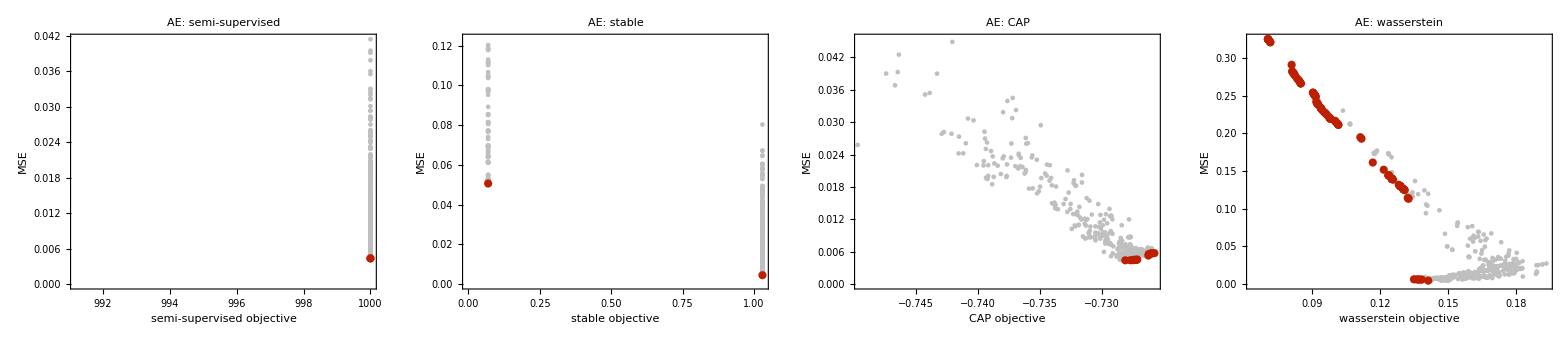

```mathematica
frontRowAE = modelFrontRow[rebuttalFrontsDir, "ae", "AE"]
Export[rebuttalOutDir <> "fronts_ae" <> rebuttalTierSuffix <> ".svg", frontRowAE, "SVG"];
Export[rebuttalOutDir <> "fronts_ae" <> rebuttalTierSuffix <> ".pdf", frontRowAE, "PDF"];
```

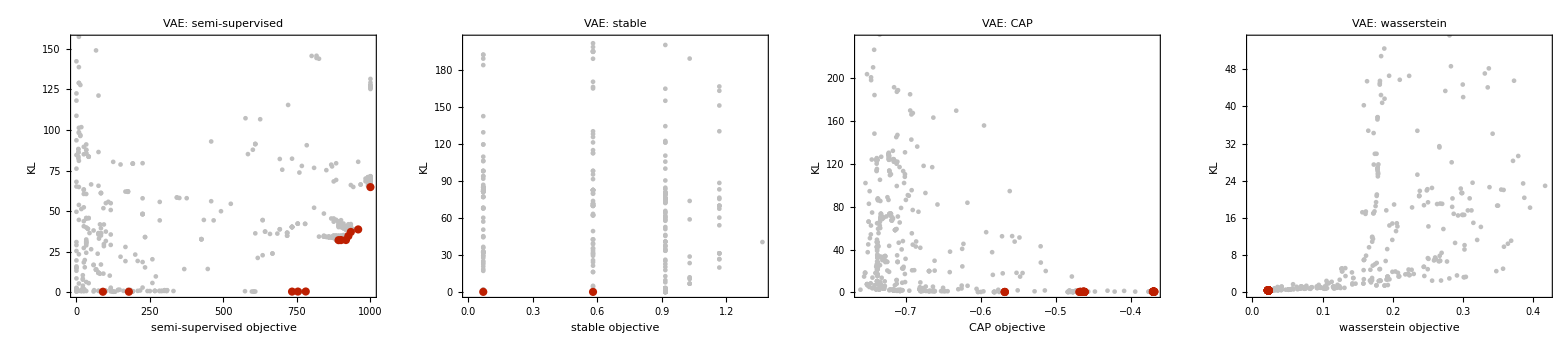

```mathematica
frontRowVAE = modelFrontRow[rebuttalFrontsDir, "vae", "VAE"]
Export[rebuttalOutDir <> "fronts_vae" <> rebuttalTierSuffix <> ".svg", frontRowVAE, "SVG"];
Export[rebuttalOutDir <> "fronts_vae" <> rebuttalTierSuffix <> ".pdf", frontRowVAE, "PDF"];
```

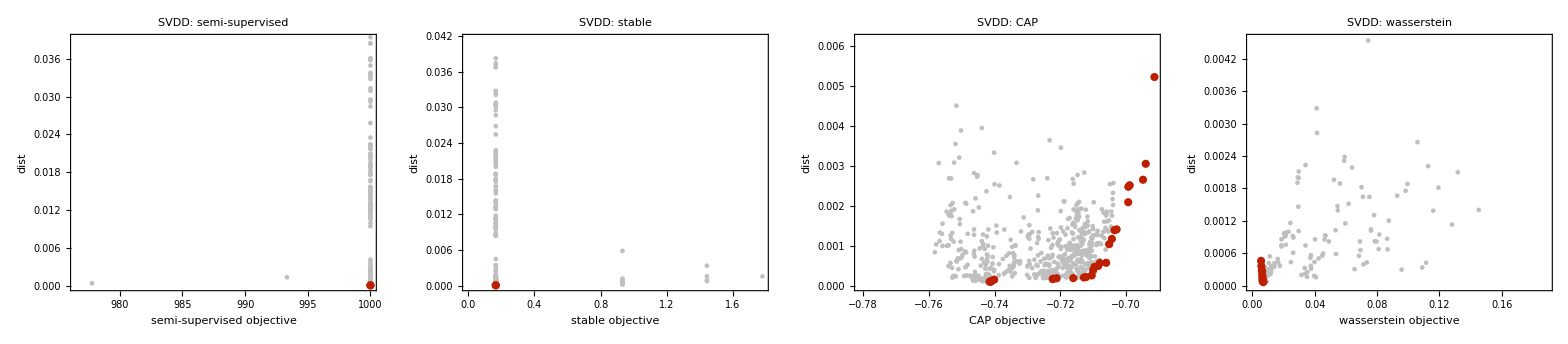

```mathematica
frontRowSVDD = modelFrontRow[rebuttalFrontsDir, "svdd", "SVDD"]
Export[rebuttalOutDir <> "fronts_svdd" <> rebuttalTierSuffix <> ".svg", frontRowSVDD, "SVG"];
Export[rebuttalOutDir <> "fronts_svdd" <> rebuttalTierSuffix <> ".pdf", frontRowSVDD, "PDF"];
```

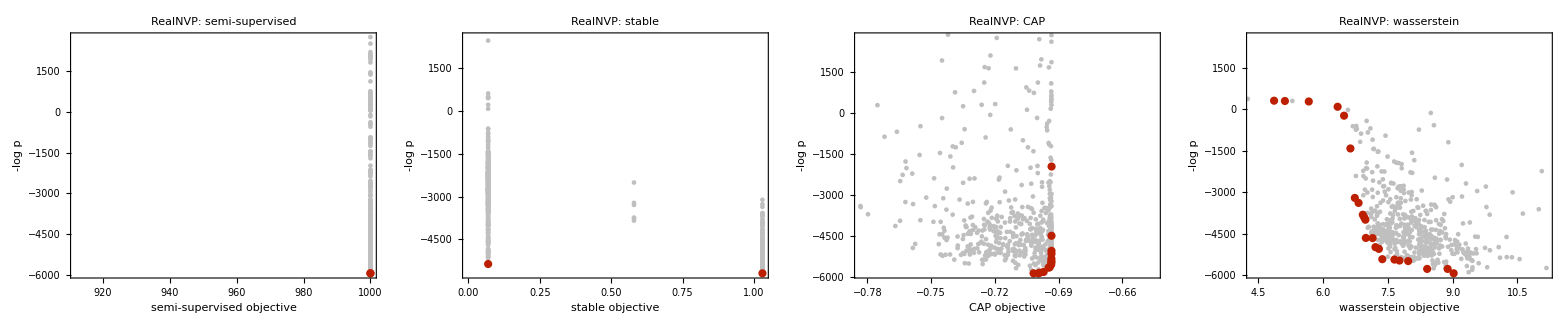

```mathematica
frontRowRealNVP = modelFrontRow[rebuttalFrontsDir, "realnvp", "RealNVP"]
Export[rebuttalOutDir <> "fronts_realnvp" <> rebuttalTierSuffix <> ".svg", frontRowRealNVP, "SVG"];
Export[rebuttalOutDir <> "fronts_realnvp" <> rebuttalTierSuffix <> ".pdf", frontRowRealNVP, "PDF"];
```

## Legacy Pareto Point Selection (by hand)

```mathematica
robustadArchitectures = Association["AE" -> Association["semisupervised" -> {100., 100., 100., 100., 100., 100.}, "CAP" -> {43.33, 100., 95., 100., 98.89, 94.67}, "stable" -> {25., 61.67, 53.33, 78.33, 93.33, 72.}, "wasserstein" -> {30., 65., 41.67, 75., 77.78, 45.33}], "VAE" -> Association["semisupervised" -> {85.33, 100., 98.33, 100., 100., 73.33}, "CAP" -> {22.67, 67.78, 60., 50., 21.67, 20.}, "stable" -> {20., 62.22, 58.33, 45., 18.33, 20.}, "wasserstein" -> {20., 60., 58.33, 45., 18.33, 20.}], "SVDD" -> Association["semisupervised" -> {100., 100., 100., 100., 100., 100.}, "CAP" -> {90.67, 100., 100., 71.67, 100., 100.}, "stable" -> {100., 100., 100., 100., 100., 100.}, "wasserstein" -> {100., 100., 100., 100., 100., 100.}], "RealNVP" -> Association["semisupervised" -> {100., 100., 100., 100., 100., 100.}, "CAP" -> {100., 100., 100., 100., 100., 100.}, "stable" -> {100., 100., 100., 100., 100., 100.}, "wasserstein" -> {92., 97.78, 98.33, 98.33, 100., 45.}]]; 

robustadTableTex = BuildLatexTableCompactAsymCollapse[robustadArchitectures, 10000, 0.05, 2];
printTable[robustadTableTex];
printTable[BuildMarkdownTableCompactAsymCollapse[robustadArchitectures, 10000, 0.05, 2]];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 100.00 & 88.65 & 63.94 & 55.80 & $24.71^{+9.52}_{-9.35}$ & 0.250 & $32.85^{+12.04}_{-11.37}$ & 0.250 \\
VAE & 92.83 & 40.35 & 37.31 & 36.94 & $3.04^{+1.50}_{-1.48}$ & 0.375 & $3.41^{+2.04}_{-1.85}$ & 0.375 \\
SVDD & 100.00 & 93.72 & 100.00 & 100.00 & $-6.28^{+6.28}_{-9.44}$ & 1.000 & $-6.28^{+6.28}_{-9.44}$ & 1.000 \\
RealNVP & 100.00 & 100.00 & 100.00 & 88.57 & $0.00^{+0.00}_{-0.00}$ & 1.000 & $11.43^{+17.96}_{-10.22}$ & 0.375 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 100.00 | 88.65 | 63.94 | 55.80 | $24.71^{+9.35}_{-9.52}$ | 0.250 | $32.85^{+11.82}_{-11.37}$ | 0.250 |
| VAE | 92.83 | 40.35 | 37.31 | 36.94 | $3.04^{+1.48}_{-1.48}$ | 0.375 | $3.41^{+2.04}_{-1.85}$ | 0.375 |
| SVDD | 100.00 | 93.72 | 100.00 | 100.00 | $-6.28^{+6.28}_{-9.44}$ | 1.000 | $-6.28^{+6.28}_{-9.44}$ | 1.000 |
| RealNVP | 100.00 | 100.00 | 100.00 | 88.57 | $0.00^{+0.00}_{-0.00}$ | 1.000 | $11.43^{+17.96}_{-10.22}$ | 0.375 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

```mathematica
robustadAUPRCArchitectures = Association["AE" -> Association["semisupervised" -> {100., 100., 100., 100., 100., 100.}, "CAP" -> {99.4, 99.84, 100., 99.45, 100., 87.68}, "stable" -> {96.3, 99.23, 96.49, 91.6, 93.5, 77.32}, "wasserstein" -> {90.01, 97.17, 95.79, 85.72, 94.09, 82.26}], "VAE" -> Association["semisupervised" -> {99.39, 100., 99.95, 100., 100., 97.32}, "CAP" -> {83.87, 95.36, 91.79, 88.6, 77.1, 75.13}, "stable" -> {82.17, 94.75, 91.27, 86.88, 73.95, 74.56}, "wasserstein" -> {81.64, 94.59, 91.23, 86.61, 73.22, 74.55}], "SVDD" -> Association["semisupervised" -> {100., 100., 100., 100., 100., 100.}, "CAP" -> {99.98, 99.99, 100., 99.6, 100., 99.89}, "stable" -> {100., 100., 100., 100., 100., 100.}, "wasserstein" -> {100., 100., 100., 100., 100., 100.}], "RealNVP" -> Association["semisupervised" -> {80.65, 83.33, 76.92, 76.92, 76.92, 76.92}, "CAP" -> {100., 100., 100., 100., 100., 100.}, "stable" -> {98.68, 98.9, 98.36, 98.36, 98.36, 98.36}, "wasserstein" -> {80.65, 83.33, 76.92, 76.92, 76.92, 76.92}]]; 

(* AUPRC table. The fire-on-everything guard is switched off here: a
   saturated AUPRC column means perfect separation, not a degenerate
   detector, so it must not be dashed out. *)
Block[{$degenerateGuard = False},
  printTable[BuildLatexTableCompactAsymCollapse[robustadAUPRCArchitectures, 10000, 0.05, 2]];
  printTable[BuildMarkdownTableCompactAsymCollapse[robustadAUPRCArchitectures, 10000, 0.05, 2]];
]
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 100.00 & 97.73 & 92.41 & 90.84 & $5.32^{+2.69}_{-2.60}$ & 0.250 & $6.89^{+3.09}_{-2.65}$ & 0.250 \\
VAE & 99.44 & 85.31 & 83.93 & 83.64 & $1.38^{+0.86}_{-0.64}$ & 0.250 & $1.67^{+1.06}_{-0.83}$ & 0.250 \\
SVDD & 100.00 & 99.91 & 100.00 & 100.00 & $-0.09^{+0.09}_{-0.13}$ & 0.250 & $-0.09^{+0.09}_{-0.13}$ & 0.250 \\
RealNVP & 78.61 & 100.00 & 98.50 & 78.61 & $1.50^{+0.14}_{-0.18}$ & 0.250 & $21.39^{+1.69}_{-2.14}$ & 0.250 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 100.00 | 97.73 | 92.41 | 90.84 | $5.32^{+2.69}_{-2.54}$ | 0.250 | $6.89^{+3.15}_{-2.64}$ | 0.250 |
| VAE | 99.44 | 85.31 | 83.93 | 83.64 | $1.38^{+0.85}_{-0.64}$ | 0.250 | $1.67^{+1.03}_{-0.83}$ | 0.250 |
| SVDD | 100.00 | 99.91 | 100.00 | 100.00 | $-0.09^{+0.08}_{-0.13}$ | 0.250 | $-0.09^{+0.09}_{-0.13}$ | 0.250 |
| RealNVP | 78.61 | 100.00 | 98.50 | 78.61 | $1.50^{+0.14}_{-0.18}$ | 0.250 | $21.39^{+1.69}_{-2.14}$ | 0.250 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

```mathematica
(* Axis 2: AUPRC comparison summary; guard off for the same reason. *)
Block[{$degenerateGuard = False},
  printTable[MetricAxisSummary[robustadAUPRCArchitectures, "AUPRC"]];
]
```

Axis 2 (AUPRC) summary -- star = Holm-adjusted p < 0.05, family = this table:
| Arch. | CAP | d CAP-Stable (p) | d CAP-W1 (p) |
|---|---|---|---|
| AE | 97.73 (best) | 5.32 (0.250) | 6.89 (0.250) |
| VAE | 85.31 (best) | 1.38 (0.250) | 1.67 (0.250) |
| SVDD | 99.91 | -0.09 (0.250) | -0.09 (0.250) |
| RealNVP | 100.00 (best) | 1.50 (0.250) | 21.39 (0.250) |
counts: CAP best point estimate in 3/4 cells; significant for CAP: 0, against: 0, n/a: 0 (of 8 comparisons).

## Best Q'

```mathematica
bestqGroups = rulePickArrays[rebuttalModelExps, bestQPick];
bestqTabRows = HolmAdjustRows[BuildArchitectureRowsCompactCollapse[
   toLegacyGroups[bestqGroups], 10000, 0.05]];
printTable[LatexTableFromRows[bestqTabRows, 2]];
printTable[MarkdownTableFromRows[bestqTabRows, 2]];
```

note: no harvest CSV for robustad_dte_pareto -- omitting this model.

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 100.00 & 87.69 & 100.00 & 72.44 & $-12.31^{+9.91}_{-13.89}$ & 0.250 & $15.24^{+8.37}_{-8.37}$ & 0.250 \\
VAE & 100.00 & 24.17 & 24.43 & 23.76 & $-0.26^{+19.91}_{-19.91}$ & 1.000 & $0.41^{+21.11}_{-20.74}$ & 1.000 \\
SVDD & 100.00 & 66.04 & 100.00 & 100.00 & $-33.96^{+14.43}_{-17.37}$ & 0.250 & $-33.96^{+14.24}_{-17.37}$ & 0.250 \\
RealNVP & 100.00 & 64.17 & 100.00 & 99.50 & $-35.83^{+24.44}_{-26.11}$ & 0.250 & $-35.33^{+23.94}_{-25.83}$ & 0.250 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | 100.00 | 87.69 | 100.00 | 72.44 | $-12.31^{+9.91}_{-13.89}$ | 0.250 | $15.24^{+8.37}_{-8.37}$ | 0.250 |
| VAE | 100.00 | 24.17 | 24.43 | 23.76 | $-0.26^{+19.91}_{-19.91}$ | 1.000 | $0.41^{+21.11}_{-20.74}$ | 1.000 |
| SVDD | 100.00 | 66.04 | 100.00 | 100.00 | $-33.96^{+14.43}_{-17.37}$ | 0.250 | $-33.96^{+14.24}_{-17.37}$ | 0.250 |
| RealNVP | 100.00 | 64.17 | 100.00 | 99.50 | $-35.83^{+24.44}_{-26.11}$ | 0.250 | $-35.33^{+23.94}_{-25.83}$ | 0.250 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

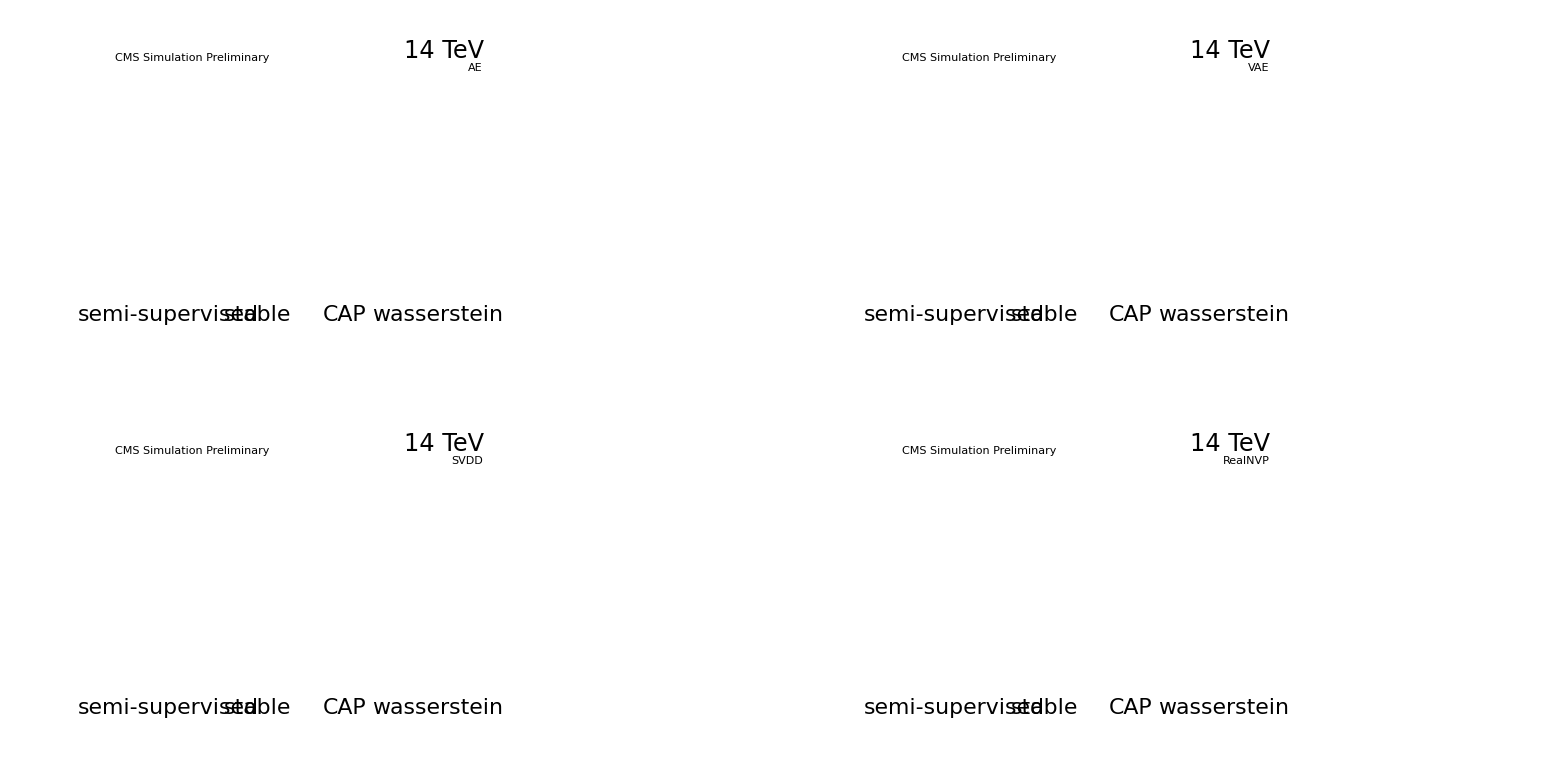

```mathematica
bestqGroups = rulePickArrays[rebuttalModelExps, bestQPick];
bestqPlot = makeRuleBoxGrid[dropEmptyModels[bestqGroups], 2]
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".svg", bestqPlot, "SVG"];
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".pdf", bestqPlot, "PDF"];
Export[rebuttalOutDir <> "grouped_bestq" <> rebuttalTierSuffix <> ".jpeg", bestqPlot, "JPEG"];
```

## Pareto Knee Selection

```mathematica
kneeGroups = rulePickArrays[rebuttalModelExps, kneePick];
kneeTabRows = HolmAdjustRows[BuildArchitectureRowsCompactCollapse[
   toLegacyGroups[kneeGroups], 10000, 0.05]];
printTable[LatexTableFromRows[kneeTabRows, 2]];
printTable[MarkdownTableFromRows[kneeTabRows, 2]];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & no-pick & 88.46 & no-pick & 72.44 & n/a & n/a & $16.02^{+8.43}_{-8.61}$ & 0.125 \\
VAE & 100.00 & 16.61 & no-pick & 25.48 & n/a & n/a & $-8.87^{+19.44}_{-18.72}$ & 0.875 \\
SVDD & no-pick & 99.50 & no-pick & 100.00 & n/a & n/a & $-0.50^{+0.50}_{-0.61}$ & 0.875 \\
RealNVP & no-pick & 70.69 & no-pick & 100.00 & n/a & n/a & $-29.31^{+18.11}_{-23.46}$ & 0.125 \\
\bottomrule
\end{tabular}
% legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

| Arch. | Semi | CAP | Stable | W1 | CAP-Stable | p | CAP-W1 | p |
|---|---|---|---|---|---|---|---|---|
| AE | no-pick | 88.46 | no-pick | 72.44 | n/a | n/a | $16.02^{+8.43}_{-8.61}$ | 0.125 |
| VAE | 100.00 | 16.61 | no-pick | 25.48 | n/a | n/a | $-8.87^{+19.44}_{-18.72}$ | 0.875 |
| SVDD | no-pick | 99.50 | no-pick | 100.00 | n/a | n/a | $-0.50^{+0.50}_{-0.61}$ | 0.875 |
| RealNVP | no-pick | 70.69 | no-pick | 100.00 | n/a | n/a | $-29.31^{+18.11}_{-23.46}$ | 0.125 |

legend: no-pick = rule could not select from this front (knee needs >= 3 Pareto points, best-Q' needs >= 1); coll = method collapsed (all-zero) or excluded by the saturation guard; n/a = comparison not computable (a required side is missing).

```mathematica
kneeGroups = rulePickArrays[rebuttalModelExps, kneePick];
kneePlot = makeRuleBoxGrid[dropEmptyModels[kneeGroups], 2]
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".svg", kneePlot, "SVG"];
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".pdf", kneePlot, "PDF"];
Export[rebuttalOutDir <> "grouped_knee" <> rebuttalTierSuffix <> ".jpeg", kneePlot, "JPEG"];
```

-Graphics-

## Spearman Ranking

```mathematica
printTable[spearmanMatrixLatex[rebuttalModelExps]];
printTable[spearmanMatrixMarkdown[rebuttalModelExps]];
```

\begin{tabular}{lcccc}
\toprule
Arch. & Semi & CAP & Stable & W1 \\
\midrule
AE & n/a (1) & 0.23 (13) & n/a (2) & -0.75 (12) \\
VAE & 0.96 (12) & 0.61 (12) & n/a (2) & -0.91 (13) \\
SVDD & n/a (1) & -0.19 (26) & n/a (1) & n/a (14) \\
RealNVP & n/a (1) & -0.10 (17) & n/a (2) & 0.50 (13) \\
DTE & no-pick & no-pick & no-pick & no-pick \\
\bottomrule
\end{tabular}

| Arch. | Semi | CAP | Stable | W1 |
|---|---|---|---|---|
| AE | n/a (1) | 0.23 (13) | n/a (2) | -0.75 (12) |
| VAE | 0.96 (12) | 0.61 (12) | n/a (2) | -0.91 (13) |
| SVDD | n/a (1) | -0.19 (26) | n/a (1) | n/a (14) |
| RealNVP | n/a (1) | -0.10 (17) | n/a (2) | 0.50 (13) |
| DTE | no-pick | no-pick | no-pick | no-pick |